```mathematica
f[x_]:=Piecewise[{{1,0<x<1},{-1,1<x<2}}]
```

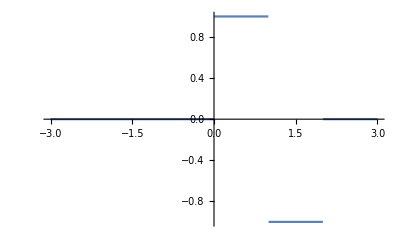

```mathematica
Plot[{f[x]},{x,-3,3}]
```

```mathematica
g[w_]:=√(2/π)∫_0^∞ (f[x]Cos[w*x])ⅆx
```

```mathematica
g[w]
```

-(2 √(2/π) (-Sin[w]+Cos[w] Sin[w]))/w

```mathematica
m[w_]:=√(2/π)∫_0^∞ (f[x]Sin[w*x])ⅆx
```

```mathematica
m[w]
```

(√(2/π) (1-2 Cos[w]+Cos[2 w]))/w

```mathematica
ff=1/(√(2*π))∫_0^40 (g[w]Cos[w*x]+m[w]Sin[w*x])ⅆw
```

(2 SinIntegral[40-40 x]+SinIntegral[40 (-2+x)]+SinIntegral[40 x])/π

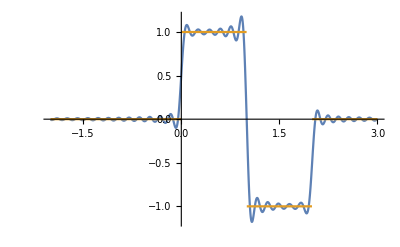

```mathematica
Plot[{ff, f[x]},{x,-2,3}]
```

```mathematica
fff[x_]:=Piecewise[{{1-x^2,-1<x<1}}]
```

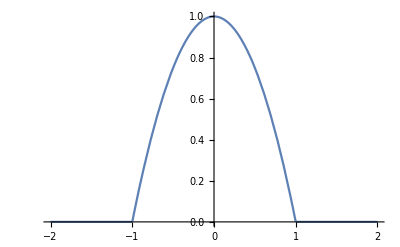

```mathematica
Plot[{fff[x]},{x, -2,2}]
```

```mathematica
g[w_]:=√(2/π)∫_(-∞)^∞ (fff[x]Cos[w*x])ⅆx
```

```mathematica
g[w]
```

-(4 √(2/π) (w Cos[w]-Sin[w]))/w^3

```mathematica
m[w_]:=√(2/π)∫_(-∞)^∞ (fff[x]Sin[w*x])ⅆx

m[x]
```

(2 Cos[1]-√(2 π) FresnelC[√(2/π)]+2 √(2 π) FresnelS[√(2/π)])/(√(2 π))

```mathematica
ff=1/(√(2*π))∫_0^20 (g[w]Cos[w*x]+m[w]Sin[w*x])ⅆw
```

(Cos[20 x] (20 Cos[20]-Sin[20])+20 x Sin[20] Sin[20 x]-200 (-1+x^2) (SinIntegral[20-20 x]+SinIntegral[20 (1+x)]))/(200 π)

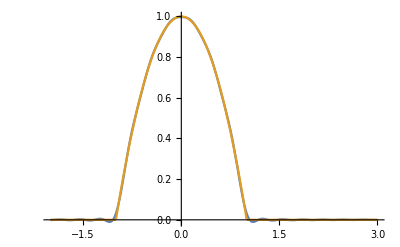

```mathematica
Plot[{ff, fff[x]},{x,-2,3}]
```

```mathematica
fff'
```

Piecewise[{{0, #1<-1}, {-2 #1, -1<#1<1}, {0, #1>1}, {Indeterminate, True}}]&

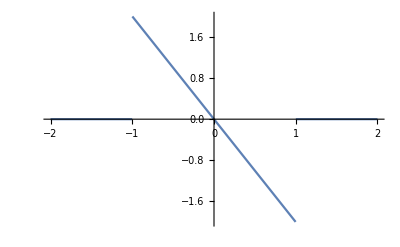

```mathematica
Plot[fff'[x],{x,-2,2}]
```